## Images

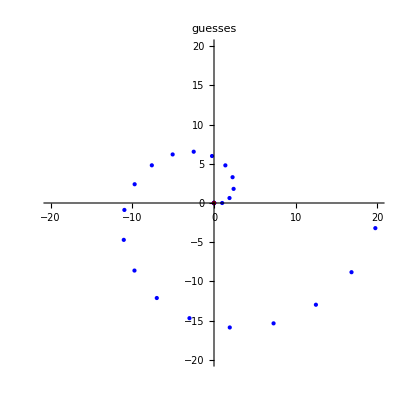

```mathematica
p1=Show[ListPolarPlot[Riffle[Table[n,{n,20}],0],PlotStyle->{Blue,PointSize[Large]},Mesh->All,PlotRange->All,PlotLabel->Style["guesses",Large,Blue]],Graphics[{PointSize[Large],Red,Point[{0,0}]}]]
```

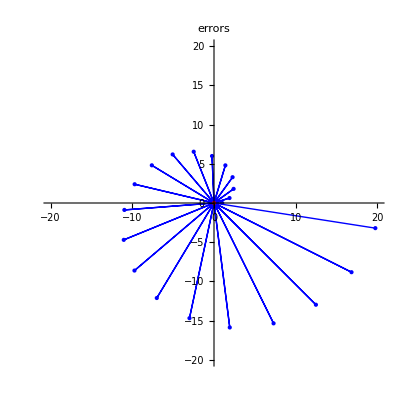

```mathematica
p2=Show[ListPolarPlot[Riffle[Table[n,{n,20}],0],PlotStyle->{Blue,PointSize[Small]},Joined->True,Mesh->All,PlotRange->All,PlotLabel->Style["errors",Large,Blue]],Graphics[{PointSize[Large],Red,Point[{0,0}]}]]
```

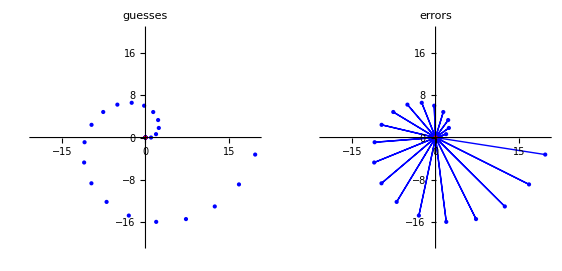

```mathematica
GraphicsGrid[{{p1,p2}}]
```

## Lab Exercise (i) (solution)

## Intializing the Guess and Objective

```mathematica
Off[General::spell]
Off[General::spell1]
Clear[f]
nb=SelectedNotebook[ ];
inx=.4;
iny=.7;
fi=x^3-x y^2+y^3-y+1;
gi=0;
(*The next commands build partial derivatives that can be used in the iteration function (and an exact line search) while accepting current guesses in the argument later*)
fy[x_,y_]=D[f[x,y],y];
fx[x_,y_]=D[f[x,y],x];
fxx[x_,y_]=D[fx[x,y],x];
fxy[x_,y_]=D[fx[x,y],y];
fyx[x_,y_]=D[fy[x,y],x];
fyy[x_,y_]=D[fy[x,y],y];
PasteButton[Defer[fx[x,y]]];
PasteButton[Defer[fy[x,y]]];
PasteButton[Defer[fxx[x,y]]];
PasteButton[Defer[fxy[x,y]]];
PasteButton[Defer[fyx[x,y]]];
PasteButton[Defer[fyy[x,y]]];
(*The next command finds the exact line search step of f from {xo,yo} in the direction {d1,d2}*)
ExactStep[xo_,yo_,{d1_,d2_}]:=Module[{a,x,y,min},min=Minimize[f[xo+a d1,yo+a d2],a];a/.min[[2]]]
(*The next command finds the solution to the SQP quadratic program with multiplier lam at (xo,yo)*)SQP[xo_,yo_,lam_]:=Module[{L,TQ,x,y,min},L[x_,y_]:=f[x,y]-lam g[x,y];TQ[x_,y_]=L[xo,yo]+Derivative[1,0][L][xo,yo](x-xo)+Derivative[0,1][L][xo,yo](y-yo)+1/2{x-xo,y-yo}.{{Derivative[2,0][L][xo,yo],Derivative[1,1][L][xo,yo]},{Derivative[1,1][L][xo,yo],Derivative[0,2][L][xo,yo]}}.{x-xo,y-yo};min=Minimize[{TQ[x,y],g[xo,yo]+Derivative[1,0][g][xo,yo](x-xo)+Derivative[0,1][g][xo,yo](y-yo)≥0},{x,y}];{Replace[x,min[[2]]],Replace[y,min[[2]]]}]
(*The next command returns the new multiplier from the old lam associated with the old guess (xo,yo)*)SQPlam[xo_,yo_,lam_]:=Module[{L,TQ,x,y,min},L[x_,y_]:=f[x,y]-lam g[x,y];(Derivative[1,0][L][xo,yo]+1/2 (2 (SQP[xo,yo,lam][[2]]-yo) Derivative[1,1][L][xo,yo]+2 (SQP[xo,yo,lam][[1]]-xo) Derivative[2,0][L][xo,yo]))/(Derivative[1,0][g][xo,yo])+lam]
(*The next command iterates the iteration function once and updates the list of guesses*)
IterateOpt[{xo_,yo_}]:=Module[{xn,yn},{xn,yn}=Evaluate[G[xo,yo]];guess=AppendTo[guess,N[{xn,yn}]];]
(*The next command draws the contour plot of the objective with the guesslist and constraint curve--if there is one--overlayed*)
VisualOpt[list_,f_,g_]:=Module[{xmax,xmin,ymax,ymin},xmax=Max[list[[All,1]]];xmin=Min[list[[All,1]]];ymax=Max[list[[All,2]]];ymin=Min[list[[All,2]]];
Grid[{{Grid[{{"newest 20 guesses"},{If[Length[list]≤19,TableForm[list],TableForm[Take[list,-20]]]}},Alignment->{Center,Center}],Show[ContourPlot[f,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->20,PlotPoints->25],Graphics[{Blue,Line[list]}],Graphics[{Blue,PointSize[Medium],Point[list]}],Graphics[{Blue,PointSize[Large],Point[First[list]]}],Graphics[{Red,PointSize[Large],Point[Last[list]]}],RegionPlot[g<0,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},PlotStyle->Opacity[.3]],ContourPlot[g,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->{0},PlotPoints->25,ContourShading->False,ContourStyle->{Thick,Blue}],Frame->True,FrameLabel->{Style["Newest guess is "Style[Last[list],Red],Medium],,Style["First guess is "Style[First[list],Blue],Medium]},ImageSize->Medium]}},ItemSize->{{15,30}},Alignment->{Center,Top},Frame->All]]
(*The next command makes a pop-up box to intiialize the method*)
Start:=Module[{},DialogInput[{Grid[{{TextCell["First Guess"]},{Grid[{{TextCell["x ="],InputField[Dynamic[inx],Number,ImageSize->30],TextCell["y ="],InputField[Dynamic[iny],Number,ImageSize->30]}}]}}],Grid[{{TextCell["Objective function"]},{TextCell["f[x,y]"],InputField[Dynamic[fi]]}}],Grid[{{TextCell["Constraint function"]},{TextCell["g[x,y]"],InputField[Dynamic[gi]],TextCell["≥ 0"]}}],
DefaultButton["Done",DialogReturn[guess={{inx,iny}};f[x_,y_]=fi;g[x_,y_]=gi;]]}]];
```

```mathematica
Start
```

```mathematica
G[x_,y_]:={x,y}+Inverse[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}].-{fx[x,y],fy[x,y]}
```

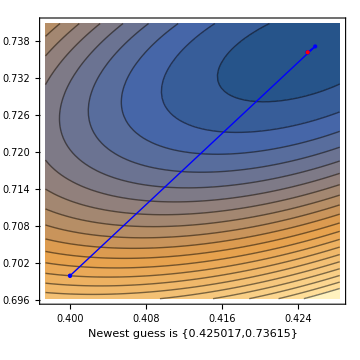
newest 20 guesses
0.4 | 0.7
0.425806 | 0.737097
0.425017 | 0.736151
0.425017 | 0.73615
0.425017 | 0.73615 | -Graphics-

```mathematica
IterateOpt[Last[guess]];Print[VisualOpt[guess,fi,gi]]
```

```mathematica
{{0.4, 0.7}, {0.4258064516129032, 0.7370967741935485}, {0.42501740543049427, 0.7361510791366905}, {0.42501665125403093, 0.7361504340338878}, {0.4250166512533082, 0.7361504340335123}}
```

#### Open this cell for details on how to extract old guesses from the full list

If at any time, you need to compute something else involving the guesses, you can extract them from the list guess in which they are stored.  For example, the x and y coordinates respectively of the newest guess are obtained by entering

```mathematica
Last[guess][[1]]
Last[guess][[2]]
```

The function Last retrieves the last element of the list (of pairs), and the [[1]] or [[2]] identifies the first or second component of the pair.

### Make a list of the differences between the guesses and the final guess (our surrogate for the target)

```mathematica
diff=guess-Table[Last[guess],{Length[guess]}]
```

{{-0.0250167,-0.0361504},{0.0007898,0.00094634},{7.54177×10^-7,6.45103×10^-7},{7.22755×10^-13,3.75477×10^-13},{0.,0.}}

### Make a list of errors

```mathematica
erlist=Map[Norm,diff];
TableForm[erlist]
```

0.0439623
0.00123262
9.92442×10^-7
8.14468×10^-13
0.

### Make a list of new errors divided by old errors

```mathematica
lin={erlist[[2]]/erlist[[1]]};
Do[lin=Append[lin,erlist[[k+1]]/erlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[lin]
```

0.028038
0.000805151
8.20671×10^-7

SUPERLINEAR ORDER OF CONVERGENCE, so try for more

### Make a list of new errors divided by old errors-squared

```mathematica
esqlist=erlist^2;
quad={erlist[[2]]/esqlist[[1]]};
Do[quad=Append[quad,erlist[[k+1]]/esqlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[quad]
```

0.637774
0.653204
0.82692

QUADRATIC ORDER OF CONVERGENCE with constant ~ 0.83

### Make a list of new errors divided by old errors-cubed

```mathematica
ecublist=erlist^3;
cubic={erlist[[2]]/ecublist[[1]]};
Do[cubic=Append[cubic,erlist[[k+1]]/ecublist[[k]]],{k,2,Length[erlist]-2}]
TableForm[cubic]
```

14.5073
529.933
833218.

NOT CUBIC ORDER OF CONVERGENCE.....so quadratic is the best we can get.

### A single table with all the quotients

```mathematica
TableForm[Transpose[{Prepend[lin,"linear error quotients"],Prepend[quad,"quadratic error quotients"],Prepend[cubic,"cubic error quotients"]}]]
```

linear error quotients | quadratic error quotients | cubic error quotients
0.028038 | 0.637774 | 14.5073
0.000805151 | 0.653204 | 529.933
8.20671×10^-7 | 0.82692 | 833218.

## Lab Exercise (ii) (solution)

## Intializing the Guess and Objective

```mathematica
Off[General::spell]
Off[General::spell1]
Clear[f]
nb=SelectedNotebook[ ];
inx=.4;
iny=.7;
fi=x^3-x y^2+y^3-y+1;
gi=0;
(*The next commands build partial derivatives that can be used in the iteration function (and an exact line search) while accepting current guesses in the argument later*)
fy[x_,y_]=D[f[x,y],y];
fx[x_,y_]=D[f[x,y],x];
fxx[x_,y_]=D[fx[x,y],x];
fxy[x_,y_]=D[fx[x,y],y];
fyx[x_,y_]=D[fy[x,y],x];
fyy[x_,y_]=D[fy[x,y],y];
PasteButton[Defer[fx[x,y]]];
PasteButton[Defer[fy[x,y]]];
PasteButton[Defer[fxx[x,y]]];
PasteButton[Defer[fxy[x,y]]];
PasteButton[Defer[fyx[x,y]]];
PasteButton[Defer[fyy[x,y]]];
(*The next command finds the exact line search step of f from {xo,yo} in the direction {d1,d2}*)
ExactStep[xo_,yo_,{d1_,d2_}]:=Module[{a,x,y,min},min=Minimize[f[xo+a d1,yo+a d2],a];a/.min[[2]]]
(*The next command finds the solution to the SQP quadratic program with multiplier lam at (xo,yo)*)SQP[xo_,yo_,lam_]:=Module[{L,TQ,x,y,min},L[x_,y_]:=f[x,y]-lam g[x,y];TQ[x_,y_]=L[xo,yo]+Derivative[1,0][L][xo,yo](x-xo)+Derivative[0,1][L][xo,yo](y-yo)+1/2{x-xo,y-yo}.{{Derivative[2,0][L][xo,yo],Derivative[1,1][L][xo,yo]},{Derivative[1,1][L][xo,yo],Derivative[0,2][L][xo,yo]}}.{x-xo,y-yo};min=Minimize[{TQ[x,y],g[xo,yo]+Derivative[1,0][g][xo,yo](x-xo)+Derivative[0,1][g][xo,yo](y-yo)≥0},{x,y}];{Replace[x,min[[2]]],Replace[y,min[[2]]]}]
(*The next command returns the new multiplier from the old lam associated with the old guess (xo,yo)*)SQPlam[xo_,yo_,lam_]:=Module[{L,TQ,x,y,min},L[x_,y_]:=f[x,y]-lam g[x,y];(Derivative[1,0][L][xo,yo]+1/2 (2 (SQP[xo,yo,lam][[2]]-yo) Derivative[1,1][L][xo,yo]+2 (SQP[xo,yo,lam][[1]]-xo) Derivative[2,0][L][xo,yo]))/(Derivative[1,0][g][xo,yo])+lam]
(*The next command iterates the iteration function once and updates the list of guesses*)
IterateOpt[{xo_,yo_}]:=Module[{xn,yn},{xn,yn}=Evaluate[G[xo,yo]];guess=AppendTo[guess,N[{xn,yn}]];]
(*The next command draws the contour plot of the objective with the guesslist and constraint curve--if there is one--overlayed*)
VisualOpt[list_,f_,g_]:=Module[{xmax,xmin,ymax,ymin},xmax=Max[list[[All,1]]];xmin=Min[list[[All,1]]];ymax=Max[list[[All,2]]];ymin=Min[list[[All,2]]];
Grid[{{Grid[{{"newest 20 guesses"},{If[Length[list]≤19,TableForm[list],TableForm[Take[list,-20]]]}},Alignment->{Center,Center}],Show[ContourPlot[f,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->20,PlotPoints->25],Graphics[{Blue,Line[list]}],Graphics[{Blue,PointSize[Medium],Point[list]}],Graphics[{Blue,PointSize[Large],Point[First[list]]}],Graphics[{Red,PointSize[Large],Point[Last[list]]}],RegionPlot[g<0,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},PlotStyle->Opacity[.3]],ContourPlot[g,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->{0},PlotPoints->25,ContourShading->False,ContourStyle->{Thick,Blue}],Frame->True,FrameLabel->{Style["Newest guess is "Style[Last[list],Red],Medium],,Style["First guess is "Style[First[list],Blue],Medium]},ImageSize->Medium]}},ItemSize->{{15,30}},Alignment->{Center,Top},Frame->All]]
(*The next command makes a pop-up box to intiialize the method*)
Start:=Module[{},DialogInput[{Grid[{{TextCell["First Guess"]},{Grid[{{TextCell["x ="],InputField[Dynamic[inx],Number,ImageSize->30],TextCell["y ="],InputField[Dynamic[iny],Number,ImageSize->30]}}]}}],Grid[{{TextCell["Objective function"]},{TextCell["f[x,y]"],InputField[Dynamic[fi]]}}],Grid[{{TextCell["Constraint function"]},{TextCell["g[x,y]"],InputField[Dynamic[gi]],TextCell["≥ 0"]}}],
DefaultButton["Done",DialogReturn[guess={{inx,iny}};f[x_,y_]=fi;g[x_,y_]=gi;]]}]];
```

```mathematica
f[x_,y_]:=(30-y)(1+10^9/((108-x)^2(30-y)^5))^(x/12)/x  ;
```

```mathematica
Start
```

```mathematica
G[x_,y_]:={x,y}+Inverse[{{fxx[x,y],fxy[x,y]},{fyx[x,y],fyy[x,y]}}].-{fx[x,y],fy[x,y]}
```

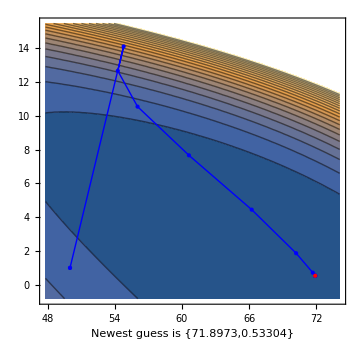
newest 20 guesses
50 | 1
54.789 | 14.121
54.2671 | 12.6756
56.0322 | 10.5546
60.6215 | 7.66995
66.2276 | 4.45039
70.1934 | 1.86954
71.6872 | 0.714
71.8931 | 0.536726
71.8973 | 0.533041
71.8973 | 0.53304
71.8973 | 0.53304 | -Graphics-

```mathematica
IterateOpt[Last[guess]];Print[VisualOpt[guess,fi,gi]]
```

```mathematica
{{50, 1}, {54.78895669305625, 14.120995441203384}, {54.267086293855435, 12.675593747024402}, {56.032165113486684, 10.554616295677333}, {60.62149331347911, 7.669950247649707}, {66.22763416050051, 4.450385950563473}, {70.19343417505402, 1.8695441664393666}, {71.68721583582288, 0.7139995157245482}, {71.8931457282602, 0.5367256074984883}, {71.89727719458055, 0.5330413075815013}, {71.89727895837811, 0.5330397282644844}, {71.89727895837844, 0.5330397282641934}}
```

#### Open this cell for details on how to extract old guesses from the full list

If at any time, you need to compute something else involving the guesses, you can extract them from the list guess in which they are stored.  For example, the x and y coordinates respectively of the newest guess are obtained by entering

```mathematica
Last[guess][[1]]
Last[guess][[2]]
```

The function Last retrieves the last element of the list (of pairs), and the [[1]] or [[2]] identifies the first or second component of the pair.

### Make a list of the differences between the guesses and the final guess (our surrogate for the target)

```mathematica
diff=guess-Table[Last[guess],{Length[guess]}]
```

{{-21.8973,0.46696},{-17.1083,13.588},{-17.6302,12.1426},{-15.8651,10.0216},{-11.2758,7.13691},{-5.66964,3.91735},{-1.70384,1.3365},{-0.210063,0.18096},{-0.00413323,0.00368588},{-1.7638×10^-6,1.57932×10^-6},{-3.2685×10^-13,2.90989×10^-13},{0.,0.}}

### Make a list of errors

```mathematica
erlist=Map[Norm,diff];
TableForm[erlist]
```

21.9023
21.8478
21.4071
18.7652
13.3446
6.89133
2.16549
0.27726
0.00553799
2.36754×10^-6
4.37613×10^-13
0.

### Make a list of new errors divided by old errors

```mathematica
lin={erlist[[2]]/erlist[[1]]};
Do[lin=Append[lin,erlist[[k+1]]/erlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[lin]
```

0.997515
0.979829
0.876588
0.711135
0.516413
0.314233
0.128036
0.019974
0.000427508
1.84839×10^-7

SUPERLINEAR ORDER OF CONVERGENCE, so try for more

### Make a list of new errors divided by old errors-squared

```mathematica
esqlist=erlist^2;
quad={erlist[[2]]/esqlist[[1]]};
Do[quad=Append[quad,erlist[[k+1]]/esqlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[quad]
```

0.0455439
0.0448479
0.0409484
0.0378964
0.0386982
0.0455983
0.0591256
0.0720408
0.0771956
0.0780724

QUADRATIC ORDER OF CONVERGENCE with constant ~ 0.078

### Make a list of new errors divided by old errors-cubed

```mathematica
ecublist=erlist^3;
cubic={erlist[[2]]/ecublist[[1]]};
Do[cubic=Append[cubic,erlist[[k+1]]/ecublist[[k]]],{k,2,Length[erlist]-2}]
TableForm[cubic]
```

0.00207942
0.00205274
0.00191284
0.0020195
0.00289991
0.00661676
0.0273036
0.259831
13.9393
32976.2

NOT CUBIC ORDER OF CONVERGENCE...so quadratic is the best we can get

### A single table with all the quotients

```mathematica
TableForm[Transpose[{Prepend[lin,"linear error quotients"],Prepend[quad,"quadratic error quotients"],Prepend[cubic,"cubic error quotients"]}]]
```

linear error quotients | quadratic error quotients | cubic error quotients
0.997515 | 0.0455439 | 0.00207942
0.979829 | 0.0448479 | 0.00205274
0.876588 | 0.0409484 | 0.00191284
0.711135 | 0.0378964 | 0.0020195
0.516413 | 0.0386982 | 0.00289991
0.314233 | 0.0455983 | 0.00661676
0.128036 | 0.0591256 | 0.0273036
0.019974 | 0.0720408 | 0.259831
0.000427508 | 0.0771956 | 13.9393
1.84839×10^-7 | 0.0780724 | 32976.2